# New Fitting using an Attenuated Sine Wave

```mathematica
ClearAll["Global`*"]
```

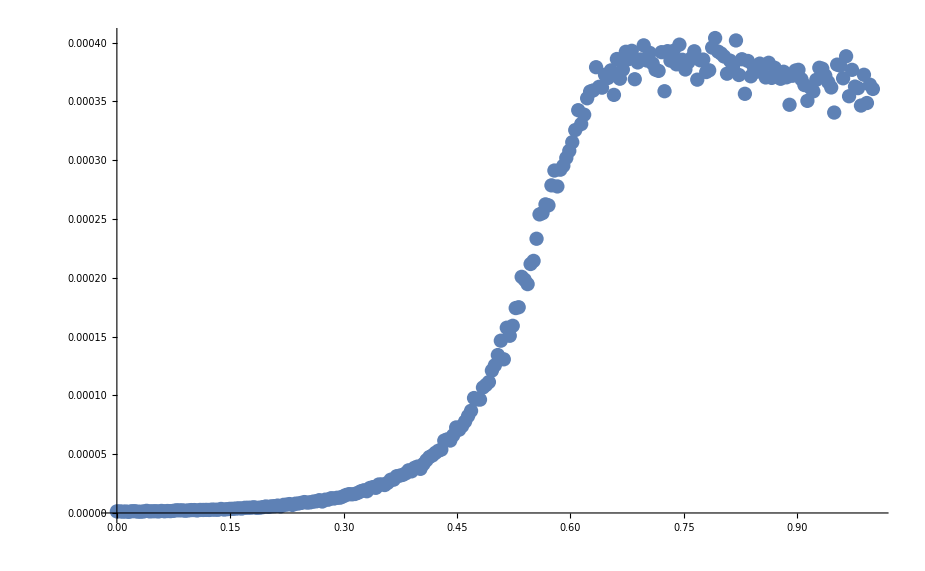

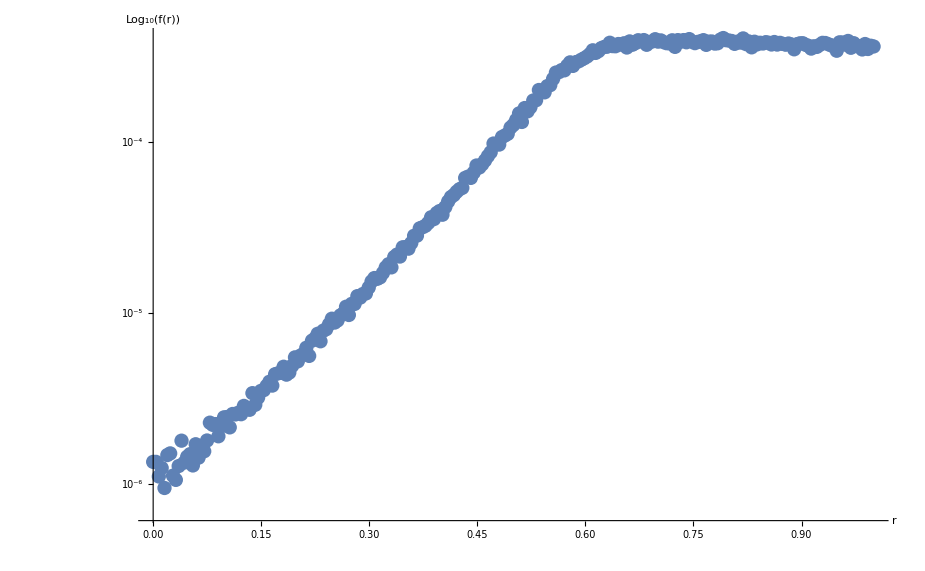

```mathematica
(* Import binary data as a 100x100 entry float3 array *)
SetDirectory[NotebookDirectory[]]; 
tableSize = 255;
rawArray= BinaryReadList["BlueNoiseRadialProfile255.complex", {"Real64","Real64"}];

radialProfileTable = Table[{i/(tableSize-1),rawArray[[Max[1,i]]][[1]]},{i,0,tableSize-1}];
logRadialProfileTable = Table[{i/(tableSize-1),Log10[rawArray[[Max[1,i]]][[1]]]},{i,0,tableSize-1}];

ListPlot[radialProfileTable]
ListPlot[logRadialProfileTable,AxesLabel->{"r","Log_10(f(r))"}];
ListLogPlot[radialProfileTable,AxesLabel->{"r","Log_10(f(r))"}]
```

## Attenuated Sine/Sigmoïd

```mathematica
cutProfile=Table[radialProfileTable[[i]],{i,140,tableSize-1}];
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{a→0.000385792,b→0.625297,c→8.02121,d→4.08171,e→-20.6229,f→0.0866656,g→-0.208976,h→-0.283764,i→0.154578,j→2.36722}

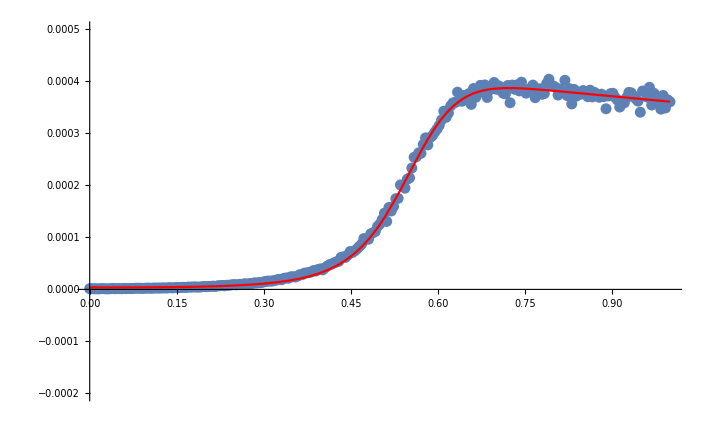

```mathematica
fittingMethod="Automatic";
model=Sin[c+d*x]/(e+f*x);
model= Exp[a+b*x]*Sin[c+d*x]/(e+f*x);
model=(a*Exp[g+h*(x+i)])/(b+c*Exp[d+e*(x^j+f)]);  (* Some sort of feng-shui sigmoïd... *)
modelFit=FindFit[cutProfile,model,{{a,0.0005},{b,1},{c,1 },{d,0},{e,-1},{f,3},{g,0},{h,-1},{i,0},{j,3}},{x},Method->fittingMethod]

model=Function[{x},Evaluate[model/.modelFit]];

Show[ 
ListPlot[radialProfileTable,PlotRange->{-0.0002,0.0005}],
 Plot[model[x],{x,0,1},PlotStyle->Red]
]
```

## Something else entirely...

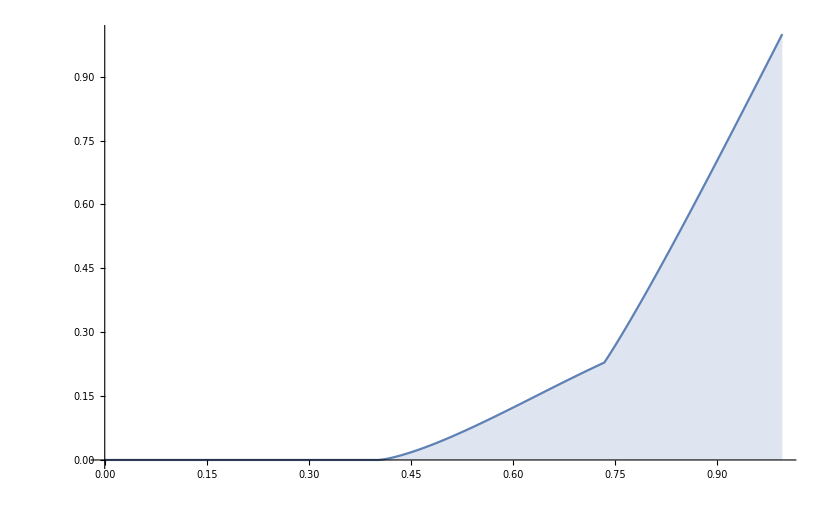

```mathematica
rawCDFArray= BinaryReadList["dickCDF.float", "Real32"];
Length[rawCDFArray];
CDFTable = Table[{(i-1)/256,rawCDFArray[[i]]},{i,1,256}];
ListPlot[CDFTable,Joined->True,Filling->Axis]
```

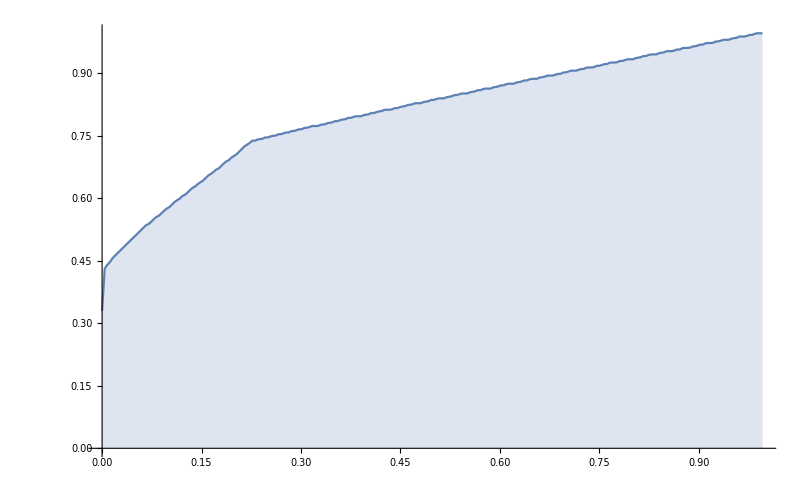

```mathematica
histoDistrib = HistogramDistribution[rawCDFArray,256];
DiscretePlot[InverseCDF[histoDistrib,x],{x,0,1,0.01},Filling->Axis];
DiscretePlot[CDF[histoDistrib,x],{x,0,1,0.01},Filling->Axis,Joined->True];
CDFTable = Table[{(i-1)/256,CDF[histoDistrib,i/256]},{i,1,256}];
ListPlot[CDFTable,Filling->Axis,Joined->True]
```

{a→0.426291,b→1.86483,c→-4.42164,d→10.1199,e→0.}

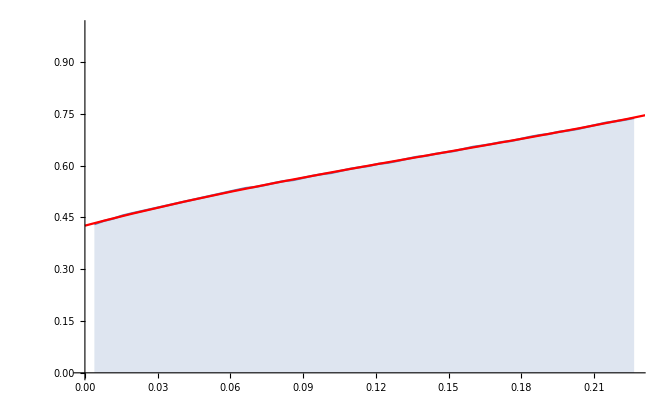

```mathematica
CDFPart0=Table[CDFTable[[i]],{i,2,59}];
ListPlot[CDFPart0,Joined->True,Filling->Axis];
model=a+b*x+c*x^2+d*x^3+e*x^4;
model=a+b*x+c*x^2+d*x^3+0*e*x^4;
modelFit=FindFit[CDFPart0,model,{{a,0.0},{b,1},{c,1 },{d,0},{e,0}},{x},Method->fittingMethod]
modelBalls=Function[{x},Evaluate[model/.modelFit]];

Show[ 
ListPlot[CDFPart0,PlotRange->{0,1}, Joined->True,Filling->Axis],
 Plot[modelBalls[x],{x,0,1},PlotStyle->Red]
]
```

{a→0.655355,b→0.378746,c→-0.035822,d→0.,e→0.}

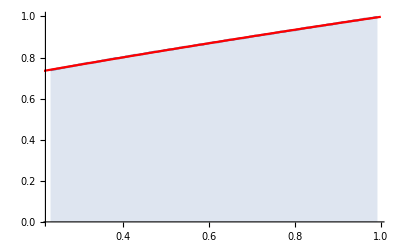

```mathematica
CDFPart1=Table[CDFTable[[i]],{i,60,255}];
ListPlot[CDFPart1,Joined->True,Filling->Axis];
model=a+b*x+c*x^2+d*x^3+e*x^4;
model=a+b*x+c*x^2;
modelFit=FindFit[CDFPart1,model,{{a,0.0},{b,1},{c,1 },{d,0},{e,0}},{x},Method->fittingMethod]
modelTip=Function[{x},Evaluate[ model/.modelFit]];

Show[ 
ListPlot[CDFPart1,PlotRange->{0,1},Joined->True,Filling->Axis],
Plot[modelTip[x],{x,0,1},PlotStyle->Red]
 ]
```

Piecewise[{{0.426291+1.86483 x-4.42164 x^2+10.1199 x^3, x<59/256}, {0.655355+0.378746 x-0.035822 x^2, x≥59/256}, {0, True}}]

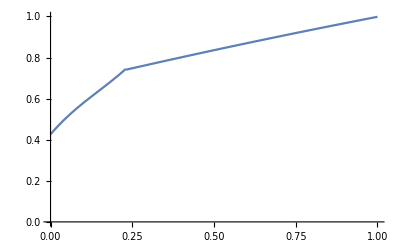

```mathematica
finalModel=Piecewise[{{modelBalls[x], x<59/256}, {modelTip[x], x≥ 59/256}}]
Plot[finalModel,{x,0,1},PlotRange->{0,1}]
```

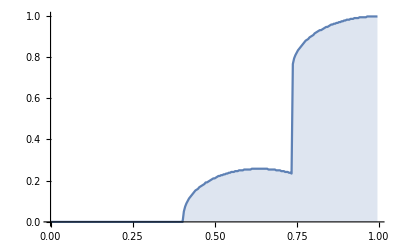

```mathematica
rawHistoArray= BinaryReadList["dickHisto.float", "Real32"];
Length[rawHistoArray];
histoDistrib = HistogramDistribution[rawHistoArray,256];
ListPlot[histoTable,Joined->True,Filling->Axis]
DiscretePlot[PDF[histoDistrib,x],{x,0,1,0.01}];
DiscretePlot[InverseCDF[histoDistrib,x],{x,0,1,0.01},Filling->Axis];
DiscretePlot[CDF[histoDistrib,x],{x,0,1,0.01},Filling->Axis];
```

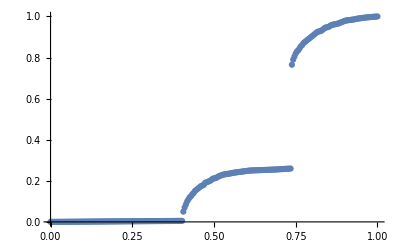

```mathematica
CDFTable = Table[{x/256,InverseCDF[histoDistrib,x/256]},{x,0,256}];
ListPlot[CDFTable]
```

{a→1.,b→38.4626,c→-11.4104,d→0.259464,e→0.,f→0.}

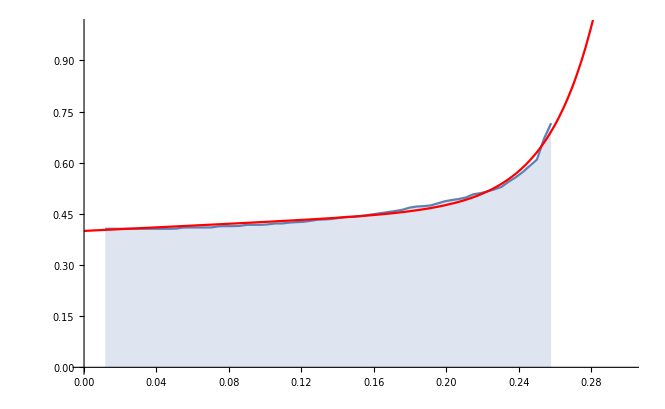

```mathematica
CDFPart0=Table[CDFTable[[i]],{i,4,67}];
ListPlot[CDFPart0,PlotRange->{{0,1},{0,1}}, Joined->True,Filling->Axis];
model=a+b*x+c*x^2+d*x^3+e*x^4;
model=a+b*x+c*x^2;
model=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
model=Max[0.4,0.4/Tanh[b*(x+0*c)]];
model=0.4+Exp[b*x+c]+d*x;
modelFit=FindFit[CDFPart0,model,{{a,1},{b,1},{c,1 },{d,2},{e,0},{f,0}},{x},Method->fittingMethod]
modelBalls=Function[{x},Evaluate[ model/.modelFit]];

Show[ 
ListPlot[CDFPart0,PlotRange->{{0,0.3},{0,1}},Joined->True,Filling->Axis],
 Plot[modelBalls[x],{x,0,1},PlotStyle->Red]
]
```

{a→-80.6072,b→525.658,c→-1352.27,d→1732.23,e→-1105.96,f→281.924}

0.737373

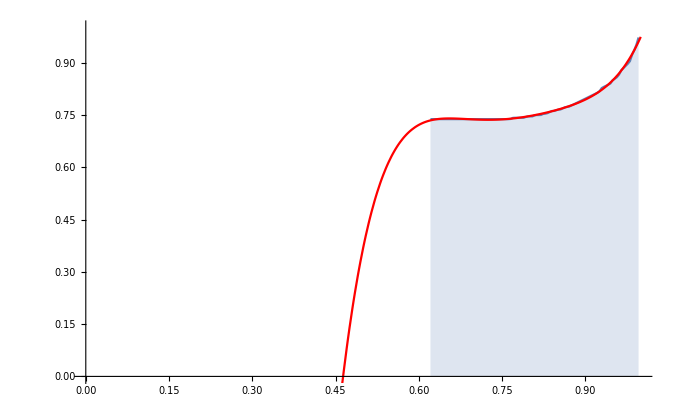

```mathematica
CDFPart1=Table[CDFTable[[i]],{i,160,256}];
ListPlot[CDFPart1,PlotRange->{{0,1},{0,1}}, Joined->True,Filling->Axis];
model=a+b*x+c*x^2+d*x^3+e*x^4;
model=a+b*x+c*x^2+d*x^3+e*x^4+f*x^5;
modelFit=FindFit[CDFPart1,model,{{a,1},{b,1},{c,1 },{d,2},{e,0},{f,0}},{x},Method->fittingMethod]
modelTip=Function[{x},Evaluate[ model/.modelFit]];
modelTip[0.7]
Show[ 
ListPlot[CDFPart1,PlotRange->{{0,1},{0,1}},Joined->True,Filling->Axis],
 Plot[modelTip[x],{x,0,1},PlotStyle->Red]
]
```

Piecewise[{{0.4+ⅇ^(-11.4104+38.4626 x)+0.259464 x, x<0.263}, {-80.6072+525.658 x-1352.27 x^2+1732.23 x^3-1105.96 x^4+281.924 x^5, x>0.7}, {0.737373, x≥0.26}, {0, True}}]

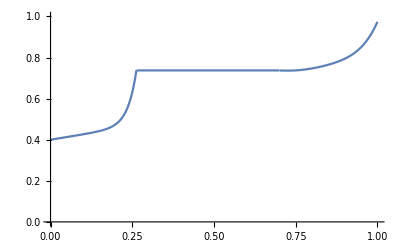

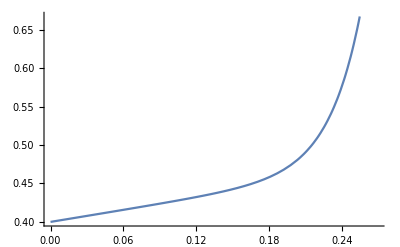

```mathematica
69.0/256;
finalModel=Piecewise[{{modelBalls[x], x<0.263}, {modelTip[x], x>0.7}, {0.7373731292608454, x≥ 0.26}}]

Plot[finalModel,{x,0,1},PlotRange->{0,1}]
Plot[modelBalls[x],{x,0,0.26953125}]
```